```mathematica
(*En esta celda leemos los 3 ficheros. Uno por cada componente del campo eléctrico*)
fileEx=OpenRead["C:\\Users\\aitor\\OneDrive\\Desktop\\TFG-AitorIngelmo\\Matematica\\Notebook NFtoNF\\microstrip_patch_antenna_Ex.txt"]
fileEy=OpenRead["C:\\Users\\aitor\\OneDrive\\Desktop\\TFG-AitorIngelmo\\Matematica\\Notebook NFtoNF\\microstrip_patch_antenna_Ey.txt"]
fileEz=OpenRead["C:\\Users\\aitor\\OneDrive\\Desktop\\TFG-AitorIngelmo\\Matematica\\Notebook NFtoNF\\microstrip_patch_antenna_Ez.txt"]
```

InputStream[C:\Users\aitor\OneDrive\Desktop\TFG-AitorIngelmo\Matematica\Notebook NFtoNF\microstrip_patch_antenna_Ex.txt,74]

InputStream[C:\Users\aitor\OneDrive\Desktop\TFG-AitorIngelmo\Matematica\Notebook NFtoNF\microstrip_patch_antenna_Ey.txt,75]

InputStream[C:\Users\aitor\OneDrive\Desktop\TFG-AitorIngelmo\Matematica\Notebook NFtoNF\microstrip_patch_antenna_Ez.txt,76]

```mathematica
(*En esta celda, leemos las 8 primeras lineas de los ficheros. Las cuales coinciden con las cabeceras del mísmo*)
Do[Read[fileEx,String],{8}]
Do[Read[fileEy,String],{8}]
Do[Read[fileEz,String],{8}]
```

```mathematica
(*En estas celdas, mostramos lo leido en la celda anterior. De esta forma, nos aseguramos de que hemos leido las cabeceras.*)
headerdataEx=Read[fileEx,String]
headerdataEy=Read[fileEy,String]
headerdataEz=Read[fileEz,String]
```

% x                       y                        z                        emw.Ex (V/m) @ freq=1.5750E9

% x                       y                        z                        emw.Ey (V/m) @ freq=1.5750E9

% x                       y                        z                        emw.Ez (V/m) @ freq=1.5750E9

```mathematica
(*En estas celda leemos todo el documento de nuevo*)
dataEx=ReadList[fileEx,String];
dataEy=ReadList[fileEy,String];
dataEz=ReadList[fileEz,String];
```

```mathematica
(*Cerramos el objeto que lee los archivos*)
Close[fileEx]
Close[fileEy]
Close[fileEz]
```

C:\Users\aitor\OneDrive\Desktop\TFG-AitorIngelmo\Matematica\Notebook NFtoNF\microstrip_patch_antenna_Ex.txt

C:\Users\aitor\OneDrive\Desktop\TFG-AitorIngelmo\Matematica\Notebook NFtoNF\microstrip_patch_antenna_Ey.txt

C:\Users\aitor\OneDrive\Desktop\TFG-AitorIngelmo\Matematica\Notebook NFtoNF\microstrip_patch_antenna_Ez.txt

```mathematica
(*Esta celda nos permite separar la cadena de texto en diversas. Emplea espacios en blanco como separado*)
datasetExSplitted=StringSplit[dataEx];
datasetEySplitted=StringSplit[dataEy];
datasetEzSplitted=StringSplit[dataEz];
```

```mathematica
(*Verificamos las dimensiones de un solo ficheros, ya que los demás son igual a este.*)
(*Dimensions[datasetExSplitted]*)
```

```mathematica
(*Esta celda es fundamental, nos permite mapear los NaN y exponenciales de los ficheros a términos equivalentes de Matematica*)
datavaluesEz=ToExpression[Map[Thread,Thread[f[datasetExSplitted,a]]]/.{a->{"E"->"*10^","i"->"I","NaN"->"0"},f->StringReplace}];
(*Tras el mapeo, comprobamos que las dimensiones siguen siendo las misma.*)
(*Dimensions[datavaluesEz]*)
```

```mathematica
(*Esta variable fija la cantidad de ?¿?¿?¿?¿*)
dimension=100
```

100

```mathematica
(*Estas lineas se usan para elminar todos los valores repetidos. Evitando tener la misma coordenada muchas veces*)
xcoordinates=Union[Part[datavaluesEz,All,1]]; 
ycoordinates=Union[Part[datavaluesEz,All,2]];
zcoordinates=Union[Part[datavaluesEz,All,3]];
```

```mathematica
(*Obtenemos los tensores de cada coordenada*)
xcoordinatesTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[1]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
ycoordinatesTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[2]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
zcoordinatesTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[3]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
```

```mathematica
datavaluesEzTensor=Table[datavaluesEz[[i+(j-1) dimension+(k-1) dimension^2]][[4]],{i,1,dimension},{j,1,dimension},{k,1,dimension}];
```

```mathematica
(*Evaluamos las dimensiones del tensor X; y del tensor de los valores del campo*)
Dimensions[xcoordinatesTensor]
Dimensions[datavaluesEzTensor]
```

{100,100,100}

{100,100,100}

```mathematica
(*Representamos el valor del índice definido por la variable "index1"*)
index1=58
zcoordinateselected1=zcoordinates[[index1]] 1.*^-3
```

58

0.015

```mathematica
(*Obtiene las coordenadas para el índice introducido previamente*)
xcoordinatesPlane1=Part[xcoordinatesTensor,All,All,index1];
ycoordinatesPlane1=Part[ycoordinatesTensor,All,All,index1];
zcoordinatesPlane1=Part[zcoordinatesTensor,All,All,index1];
```

```mathematica
datavaluesEzPlane1=Part[datavaluesEzTensor,All,All,index1];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1],PlotLegends->Automatic,ColorFunction->"DarkBands",
PlotLegends->BarLegend[{"DarkBands",{0,20}}],FrameTicks->Automatic]
```

-Graphics-

```mathematica
datavaluesEzPlane1w=Fourier[datavaluesEzPlane1,FourierParameters->{-1,1}];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1w],PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
ListPlot3D[Abs[datavaluesEzPlane1w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[10 Log[10.,Abs[datavaluesEzPlane1w]],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
deltax=(xcoordinates[[2]]-xcoordinates[[1]]) 1*^-3
```

0.002

```mathematica
deltay=(ycoordinates[[2]]-ycoordinates[[1]]) 1*^-3
```

0.002

```mathematica
Lx=(xcoordinates[[-1]]-xcoordinates[[1]]) 1*^-3
```

0.198

```mathematica
Ly=(ycoordinates[[-1]]-ycoordinates[[1]]) 1*^-3
```

0.198

```mathematica
Nx=Length[xcoordinates]
```

100

```mathematica
Ny=Length[ycoordinates]
```

100

```mathematica
deltakx=2 Pi/(deltax Nx)
```

31.4159

```mathematica
deltaky=2 Pi/(deltay Ny)
```

31.4159

```mathematica
freq=1.575*^9
```

1.575×10^9

```mathematica
c0=299792458
```

299792458

```mathematica
k0=2 Pi freq/c0
```

33.0096

```mathematica
lambda0=c0/freq
```

0.190344

```mathematica
kxcoordinatesMatrix=deltakx Table[If[i≤dimension/2,i-1,i-1-dimension],{i,1,dimension},{j,1,dimension}];
```

```mathematica
a=Table[If[i≤dimension/2,i-1,i-1-dimension],{i,1,dimension},{j,1,dimension}];
```

```mathematica
Dimensions[kxcoordinatesMatrix]
```

{100,100}

```mathematica
ListDensityPlot[kxcoordinatesMatrix,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
kycoordinatesMatrix=deltaky Table[If[j≤dimension/2,j-1,j-1-dimension],{i,1,dimension},{j,1,dimension}];
```

```mathematica
ListDensityPlot[kycoordinatesMatrix,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
k0
```

33.0096

```mathematica
w2=k0^2-kxcoordinatesMatrix^2-kycoordinatesMatrix^2;
```

```mathematica
ListDensityPlot[w2,PlotLegends->Automatic,ColorFunction->"ThermometerColors"]
```

-Graphics-

```mathematica
w=Conjugate[Sqrt[w2]];
```

```mathematica
ListDensityPlot[Re[w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Im[w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListPlot3D[Re[w],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[10 Log[10.,Re[w]+1*^-12],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics3D-

```mathematica
index2=66
```

66

```mathematica
zcoordinateselected2=zcoordinates[[index2]]*1.*^-3
```

0.031

```mathematica
phaseShift=Exp[-I w (zcoordinateselected2-zcoordinateselected1)];
```

```mathematica
datavaluesEzPlane2w=datavaluesEzPlane1w*phaseShift;
```

```mathematica
datavaluesEzReconstructedPlane2=InverseFourier[datavaluesEzPlane2w,FourierParameters->{-1,1}];
```

```mathematica
datavaluesEzReconstructedPlane2[[1]][[1]]
```

0.0047515-0.00636668 ⅈ

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane1],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Abs[datavaluesEzReconstructedPlane2],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
datavaluesEzPlane2=Part[datavaluesEzTensor,All,All,index2];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane2],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

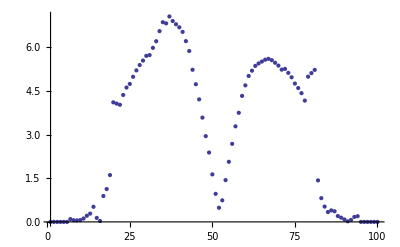

```mathematica
ListPlot[Abs[Part[datavaluesEzPlane2,30,All]],PlotRange->All]
```

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane2-datavaluesEzReconstructedPlane2],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
indicesOutsideModelledArea=Position[datavaluesEzPlane2,0];
```

```mathematica
Dimensions[indicesOutsideModelledArea]
```

{2690,2}

```mathematica
Length[indicesOutsideModelledArea]
```

2690

```mathematica
datavaluesEzReconstructedPlane2Reduced=Table[If[datavaluesEzPlane2[[i]][[j]]==0,0,datavaluesEzReconstructedPlane2[[i]][[j]]],{i,1,dimension},{j,1,dimension}];
```

```mathematica
ListDensityPlot[Abs[datavaluesEzReconstructedPlane2Reduced],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-

```mathematica
ListDensityPlot[Abs[datavaluesEzPlane2-datavaluesEzReconstructedPlane2Reduced],PlotLegends->Automatic,ColorFunction->"ThermometerColors",PlotRange->All]
```

-Graphics-